```mathematica
fa[f_,fs_]:=Module[{n},n=Floor[f/fs];Abs@If[OddQ[n],(n+1) fs-f,n fs-f]];
```

{{1,29/30},{2,14/15},{3,9/10},{4,13/15},{5,5/6},{6,4/5},{7,23/30},{8,11/15},{9,7/10},{10,2/3},{9,19/30},{8,3/5},{7,17/30},{6,8/15},{5,1/2},{4,7/15},{3,13/30},{2,2/5},{1,11/30},{0,1/3},{1,3/10},{2,4/15},{3,7/30},{4,1/5},{5,1/6},{6,2/15},{7,1/10},{8,1/15},{9,1/30},{10,0}}

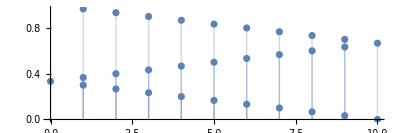

```mathematica
max=30;
Table[{fa[n,10],1-n/max},{n,1,max}]
ListPlot[Table[{fa[n,10],1-n/max},{n,1,max}],PlotRange->All,Filling->Axis,AspectRatio->1/3]
```